## Vaje 1

Avtor: Janez Šter
Datum: 19. 10. 2017

### Naloga 1

```mathematica
(1/3+1/6)^2
```

1/4

Komentar: Za potenco uporabimo znak ^.

```mathematica
3/(6/8)
```

4

```mathematica
Sin[Pi/2]
```

1

Komentar: Vgrajene funkcije v Mathematici imajo veliko začetnico, argumente pa pišemo v oglatih oklepajih.

```mathematica
E^Log[7]
```

7

### Naloga 2

```mathematica
((3+4x)/(2+5x))^2+((2+x)/(1-x))^2//Simplify
```

(2+x)^2/(-1+x)^2+(3+4 x)^2/(2+5 x)^2

Komentar: Očitno se izraza ne da kaj bistveno poenostaviti.

```mathematica
x/y+y/x+2//Simplify
```

(x+y)^2/(x y)

```mathematica
(x^2+y^2)^2-2(x y)^2//Simplify
```

x^4+y^4

Komentar: pri množenju moramo med spremenljivki x in y pisati presledek.

```mathematica
Sin[x]^2+Cos[x]^2//Simplify
```

1

```mathematica
2Sin[x]Cos[x]//Simplify
```

Sin[2 x]

S pomočjo Mathematicine pomoči (ali Googla) ugotovimo, da je ukaz za kotangens Cot.

```mathematica
Tan[Pi/8]^4+Cot[Pi/8]^4//Simplify
```

Cot[π/8]^4+Tan[π/8]^4

```mathematica
Tan[Pi/8]^4+Cot[Pi/8]^4//FullSimplify
```

34

```mathematica
Sqrt[278+42Sqrt[5]-12Sqrt[6]-28Sqrt[30]]//FullSimplify
```

3+7 √5-2 √6

### Naloga 3

Izraz nam razstavi ukaz Expand. Pri kotnih funkcijah pa je pravi ukaz TrigExpand.

```mathematica
(x+x y+y)^10//Expand
```

x^10+10 x^9 y+10 x^10 y+45 x^8 y^2+90 x^9 y^2+45 x^10 y^2+120 x^7 y^3+360 x^8 y^3+360 x^9 y^3+120 x^10 y^3+210 x^6 y^4+840 x^7 y^4+1260 x^8 y^4+840 x^9 y^4+210 x^10 y^4+252 x^5 y^5+1260 x^6 y^5+2520 x^7 y^5+2520 x^8 y^5+1260 x^9 y^5+252 x^10 y^5+210 x^4 y^6+1260 x^5 y^6+3150 x^6 y^6+4200 x^7 y^6+3150 x^8 y^6+1260 x^9 y^6+210 x^10 y^6+120 x^3 y^7+840 x^4 y^7+2520 x^5 y^7+4200 x^6 y^7+4200 x^7 y^7+2520 x^8 y^7+840 x^9 y^7+120 x^10 y^7+45 x^2 y^8+360 x^3 y^8+1260 x^4 y^8+2520 x^5 y^8+3150 x^6 y^8+2520 x^7 y^8+1260 x^8 y^8+360 x^9 y^8+45 x^10 y^8+10 x y^9+90 x^2 y^9+360 x^3 y^9+840 x^4 y^9+1260 x^5 y^9+1260 x^6 y^9+840 x^7 y^9+360 x^8 y^9+90 x^9 y^9+10 x^10 y^9+y^10+10 x y^10+45 x^2 y^10+120 x^3 y^10+210 x^4 y^10+252 x^5 y^10+210 x^6 y^10+120 x^7 y^10+45 x^8 y^10+10 x^9 y^10+x^10 y^10

```mathematica
Sin[x+y]//TrigExpand
```

Cos[y] Sin[x]+Cos[x] Sin[y]

### Naloga 4

```mathematica
a=3;
b=4;
c=6;
```

```mathematica
o=a+b+c;
s=o/2;
```

```mathematica
Sqrt[s(s-a)(s-b)(s-c)]
```

(√455)/4

Geometrijski pomen tega števila je ploščina trikotnika s stranicami a,b,c.

```mathematica
Clear[a,b,c,o,s]
```

### Naloga 5

```mathematica
s={3,2,0,0,5,13,2,-x,8}
```

{3,2,0,0,5,13,2,-x,8}

```mathematica
s[[5]]
```

5

```mathematica
s[[-1]]
```

8

Ukaz s[[-1]] vrne zadnji element (to je prvi element od desne proti levi).

### Naloga 6

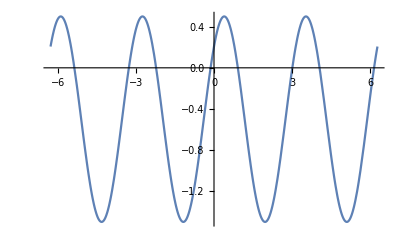

```mathematica
Plot[Sin[2x+Pi/4]-1/2,{x,-2Pi,2Pi}]
```

### Naloga 7

```mathematica
f[x_]:=5Sin[x-2]
g[x_]:=2^x-6
```

Če želimo vrisati več funkcij v isti koordinatni sistem, funkcije naštejemo v seznamu.

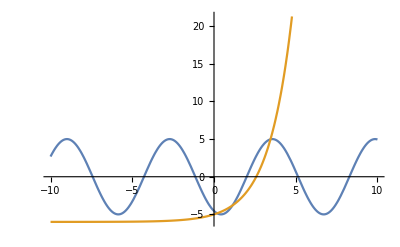

```mathematica
Plot[{f[x],g[x]},{x,-10,10}]
```

Presečišča bodo še bolje vidna, če izberemo interval [-2,4].

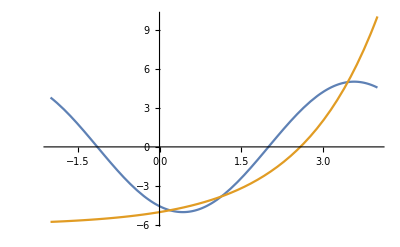

```mathematica
Plot[{f[x],g[x]},{x,-2,4}]
```

### Naloga 8

```mathematica
a=3^200+20;
b=2^300+30;
```

V Mathematici logično izjavo “enako” zapišemo z dvojnim enačajem ==, izjavo “manjši” in “večji” pa z znakoma < in >.

```mathematica
a==b
a<b
a>b
```

False

False

True

### Naloga 9

```mathematica
Solve[x^2+4x+2==0,x]
```

{{x→-2-√2},{x→-2+√2}}

```mathematica
Solve[x^2+4x+5==0,x]
```

{{x→-2-ⅈ},{x→-2+ⅈ}}

Opomba: rešitve druge enačbe so kompleksne.

### Naloga 10

```mathematica
Reduce[x^4==1,{x}]
```

x==-1||x==-ⅈ||x==ⅈ||x==1

Opomba: znak || pomeni logični “ali”. Rešitev se torej bere x=-1 ali x=-i ali x=i ali x=1.

### Naloga 11

```mathematica
f[x_]:=(x^2-(x^2)^(1/3))E^x
```

Opomba: tu je nevarnost, da (x^2)^(1/3) nadomestimo z x^(2/3) - ta dva izraza namreč za negativne x nista enaka, saj drugi izraz tam sploh ni definiran, osnova vsake potence (z neceloštevilskim eksponentom) mora biti namreč večja ali enaka 0.

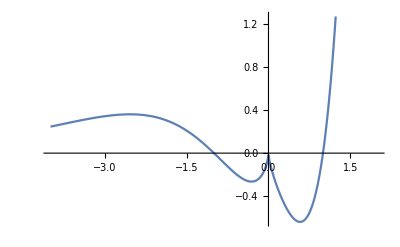

```mathematica
Plot[f[x],{x,-4,2}]
```

Glede na graf so ničle -1, 0 in 1.

```mathematica
Solve[f[x]==0,x]
```

{{x→0},{x→1}}

```mathematica
Reduce[f[x]==0,{x}]
```

x==-1||x==0||x==1

Komentar: Solve ni našel vseh ničel, Reduce pa jih je.